```mathematica
Quit
```

```mathematica
<<CliffordDecomposition`
```

# CliffordDecomposition

If you want to know the theoretical details, look for chapter 6.3 of [2]. This method was first used at [1].

## GottesmanDecompose

```mathematica
?GottesmanDecompose
```

```mathematica
Let[Qubit,S]
```

```mathematica
(*define qubits*)
$n=3;
qq=S[Range@$n,None];
```

```mathematica
(*construct random binary symplectic matrix*)
r0=RandomInteger[{0,1000},1];
got=First@BinarySymplecticGroupElements[qq,r0];
got//MatrixForm
```

(1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 1)

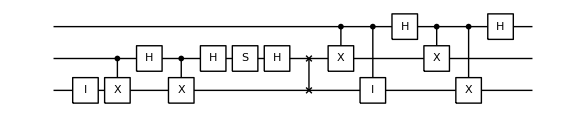

```mathematica
(*circuit*)
qcdecomp=GottesmanDecompose[got,qq]
```

```mathematica
(*Check*)
gotdecomp=GottesmanMatrix[qcdecomp//Elaborate,qq];
gotdecomp//MatrixForm
```

(1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1 | 1)

```mathematica
got-gotdecomp//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

## CliffordDecompose

```mathematica
?CliffordDecompose
```

```mathematica
Let[Qubit,S]
```

```mathematica
(*define qubits*)
$n=3;
qq=S[Range@$n,None];
```

```mathematica
(*construct random Clifford matrix*)
r0=RandomInteger[{0,1000},1];
got=First@BinarySymplecticGroupElements[qq,r0];
mat=Matrix[FromGottesmanMatrix[got,qq],qq];
mat=(ThePauli@@RandomInteger[{0,3},3]).mat;
mat//MatrixForm
```

(ⅈ/(2 √2) | -ⅈ/(2 √2) | -ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2) | -ⅈ/(2 √2)
-1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2)
-ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2) | -ⅈ/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2)
-1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2)
ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2) | ⅈ/(2 √2)
-1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2)
ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2))

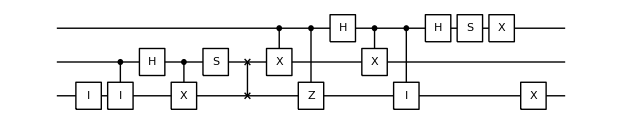

```mathematica
(*circuit*)
qcdecomp=CliffordDecompose[mat,qq]
```

```mathematica
(*Check*)
matdecomp=Matrix[qcdecomp];
matdecomp//MatrixForm
```

(1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2)
ⅈ/(2 √2) | -ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2)
-1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2)
-ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2)
ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2) | -ⅈ/(2 √2) | -ⅈ/(2 √2) | ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2)
1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2)
ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2) | -ⅈ/(2 √2) | ⅈ/(2 √2) | -ⅈ/(2 √2) | -ⅈ/(2 √2) | ⅈ/(2 √2)
1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2))

```mathematica
mat.ConjugateTranspose[matdecomp]//MatrixForm
```

(ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ)

# Reference

[1] Gottesman, Daniel. “Theory of fault-tolerant quantum computation.” Physical Review A 57.1 (1998): 127.
[2] Choi, Mahn-Soo. A Quantum Computation Workbook. Springer Nature, 2022.